```mathematica
SetDirectory[NotebookDirectory[]<>"data.06"]
```

F:\Загрузки\Диплом\Real_Sig\data.06

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogLinearPlot},PlotRange->Full,Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier",FontSize->12, Bold},ImageSize->500,PlotStyle->{Red,PointSize[0.01]}];
```

```mathematica
data=Import["v2k_bpm_xy_1.sdds","Table","HeaderLines"->13];
Data1 = Transpose[data][[3]];
Export["DataX.txt",Data1]
Data11=Take[Data1,{100,400}];
Length[Data1]
```

DataX.txt

8189

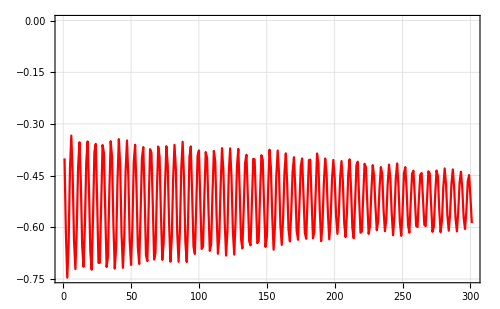

```mathematica
ListLinePlot[Data11]
```

```mathematica
AbsFourier[x_]:=Abs[Take[Fourier[x,FourierParameters->{-1, 1}],{3,Round[Length[x]/2 ]+1}]]
```

```mathematica
NumPlace[x_]:=Position[AbsFourier[x],Max[AbsFourier[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/Length[x],{b,0,Length[x]-1}]
Freq[x_]:=FreqList[x][[NumPlace[x]+2]]
```

```mathematica
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[NumPlace[x]-4;;NumPlace[x]+4]],AbsFourier[x][[NumPlace[x]-4;;NumPlace[x]+4]]}],FrameLabel->{"ν","A, mm"}]
FullPlot[x_]:=ListPlot[Transpose[{FreqList[x][[3;;Round[Length[x]/2 ]+1]],AbsFourier[x]}],FrameLabel->{"ν","A, mm"}]
```

```mathematica
HammingSig[x_]:=x*Table[(0.53836-0.46164Cos[(2Pi*k)/(Length[x]-1)]),{k,1,Length[x]}]
```

```mathematica
NuGass[x_]:=Freq[x]+(AbsFourier[x][[NumPlace[x]+1]]-AbsFourier[x][[NumPlace[x]-1]])/(2*(2*AbsFourier[x][[NumPlace[x]]]-AbsFourier[x][[NumPlace[x]+1]]-AbsFourier[x][[NumPlace[x]-1]]))/Length[x]
```

```mathematica
NAFF[x_]:=Abs[Table[Sum[x[[n]]*Exp[ⅈ*2π*β*n],{n,1,Length[x]}],{β,0,1,0.0001}]]
Nf[x_]:=Take[NAFF[x],{1000,5000}]
```

```mathematica
NumPlaceNAFF[x_]:=Position[Nf[x],Max[Nf[x]]][[1,1]]
FreqListNAFF[x_]:=Table[1.0*b/10000,{b,0,10000}]
Freql[x_]:=Take[FreqListNAFF[x],{1000,5000}]
```

```mathematica
FreqNAFF[x_]:=Freql[x][[NumPlaceNAFF[x]]]
```

```mathematica
(*TruePlotNAFF[x_]:=ListPlot[Transpose[{FreqListNAFF[x][[NumPlaceNAFF[x]-300;;Round[Length[NAFF[x]]/2 ]+1]],NAFF[x][[1;;Round[Length[NAFF[x]]/2 ]+1]]}],FrameLabel->{"ν","A, mm"},PlotStyle->PointSize[0.001]]*)
TruePlotNAFF[x_]:=ListPlot[Transpose[{Freql[x][[NumPlaceNAFF[x]-300;;NumPlaceNAFF[x]+300]],Nf[x][[NumPlaceNAFF[x]-300;;NumPlaceNAFF[x]+300]]}],FrameLabel->{"ν","A, mm"},PlotStyle->{Red,PointSize[0.005]}]
```

```mathematica
FreqSig =Freq[Data11]
```

0.169435

0.169435

0.170435

0.1709

-Graphics-

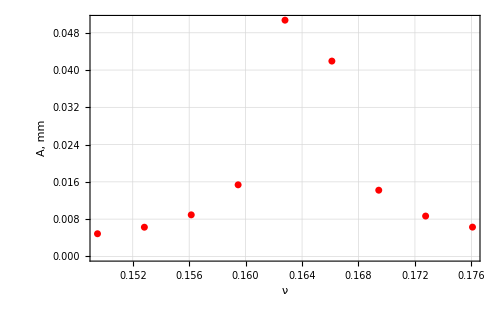

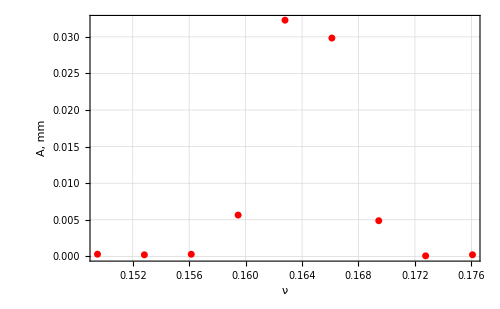

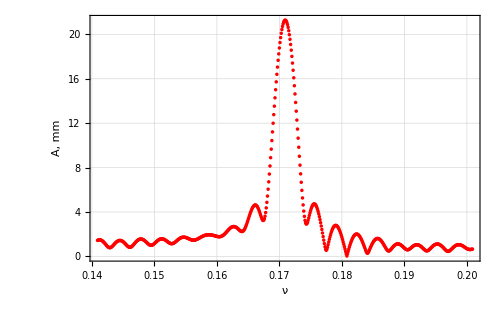

```mathematica
FreqHam=Freq[HammingSig[Data11]]
FreqGas=NuGass[Data11]
FreqNaff=FreqNAFF[Data11]
p1=ListLinePlot[Data11]
p2 = TruePlot[Data11]
p3 = TruePlot[HammingSig[Data11]]
p4=TruePlotNAFF[Data11]
```

```mathematica
Export["Graph.png",p1]
Export["Four.png",p2]
Export["Ham.png",p3]
Export["naf.png",p4]
```

Graph.png

Four.png

Ham.png

naf.png

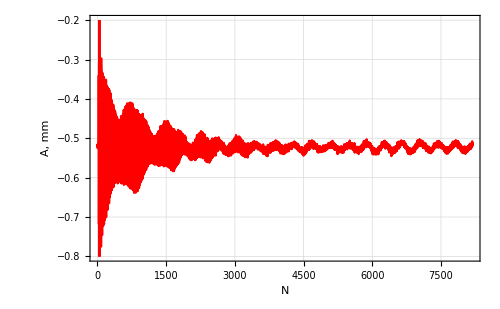

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
p1=ListLinePlot[Data1,FrameLabel->{"N","A, mm"},PlotRange->{All,{-0.2,-0.8}}]
image={{p1,p4,p2,p3}}
```

```mathematica
Export["big_image.png",image]
```

big_image.png

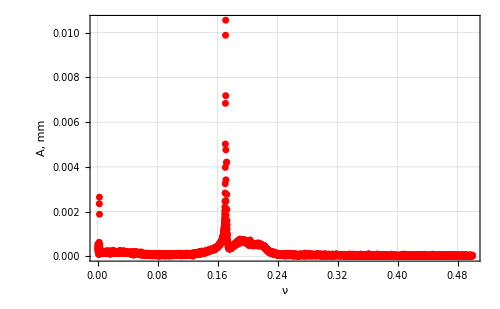

```mathematica
FullPlot[Data1]
```

```mathematica
data2=Import["v2k_bpm_xy_1.sdds","Table","HeaderLines"->13];
Data2 = Transpose[data2][[3]];
Data22=Take[Data2,{100,400}];
Length[Data22]
```

301

```mathematica
ListLinePlot[Data22]
```

-Graphics-

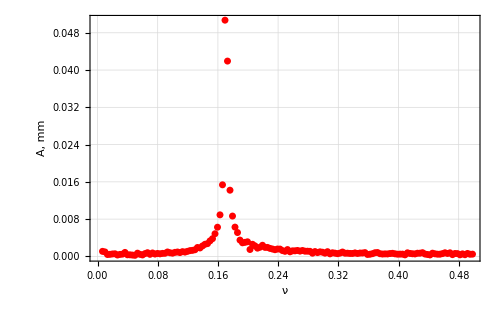

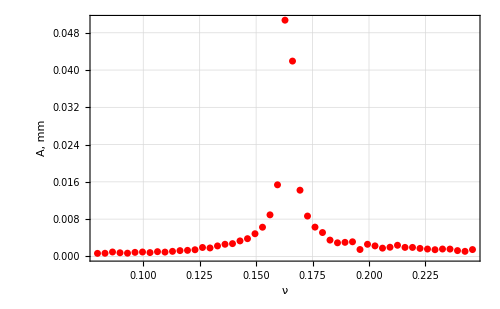

DobSig.png

```mathematica
DobSig=FullPlot[Data22]
TruePlot2[x_]:=ListPlot[Transpose[{FreqList[x][[NumPlace[x]-25;;NumPlace[x]+25]],AbsFourier[x][[NumPlace[x]-25;;NumPlace[x]+25]]}],FrameLabel->{"ν","A, mm"}]
DobSig2=TruePlot2[Data22]
Export["DobSig.png",DobSig2]
```

```mathematica
FulMasNAFFData =Transpose[{Freql[Data22][[NumPlaceNAFF[Data22]-300;;NumPlaceNAFF[Data22]+300]],Nf[Data22][[NumPlaceNAFF[Data22]-300;;NumPlaceNAFF[Data22]+300]]}];
```

0.169435

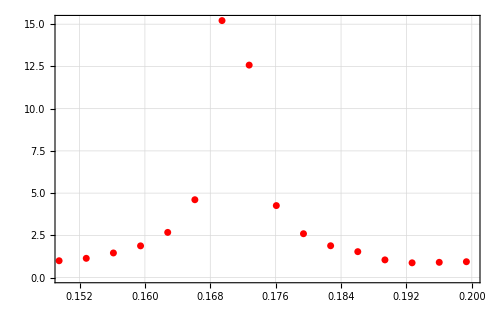

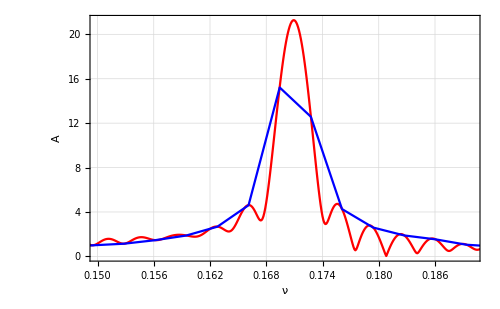

```mathematica
FulMasFourData=Transpose[{FreqList[Data22][[3;;Round[Length[Data22]/2 ]+1]],AbsFourier[Data22]*300}];
Freq[Data22]
ListPlot[FulMasFourData,PlotRange->{{0.15,0.2},All}]
NAFFEX=ListLinePlot[{FulMasNAFFData,FulMasFourData},PlotStyle->{Red,Blue},PlotRange->{{0.15,0.19},All},FrameLabel->{"ν","A"}]
```

```mathematica
Export["NAFFEX.png",NAFFEX]
```

NAFFEX.png